```mathematica
(*(
Tool for Categorising Fixed Points, see "Maternal transmission as a symbiont sieve, and the absence of lactation in male mammals"(Fagan, Constable, and Law) for details of the system and parameters.
Created by BT Fagan.
)*)
```

```mathematica
(*Tricks and Functions Employed:*)

(*There is a problem at (0, 0) and sometimes other points depending on the exact parameter values. We circumvent this by writing a substitution procedure that, if it fails, attempts to take limits instead. Note substitution is fast, while limits are slow, which is why we do not take limits everywhere. If the limit fails, then we provide a failure case.*)
limitIfSubFails[set_, limits_]:= If[Head[#]===Limit,{ComplexInfinity,ComplexInfinity},#]&/@Table[
Quiet@Check[
(*Try*)
Module[{sub}, 
sub = Chop[set[[i]]/.limits];
(*There is a rare failure case where an Indeterminate is calculated to be 0.
E.g. m = 0.79, w = 0.48, b = 3.25, d = 1.5, α = 1, β = 1, when calculating for these critical m and w specifically versus when calculating with 
minM = 0.79, maxM =0.79, stepM = 0.01,
minW = 0.01, maxW =0.48, stepW = 0.01. 
This appears to be a Mathematica problem. The limits appear to work properly, so we provide an error that will bounce us to the catch.*)
If[AnyTrue[sub, #==0.&],0^0, sub]
],
(*Catch*)
Limit[set[[i]], limits]
],{i,1,Length[set]}]

(*For Stability Analysis, we re-use code from Wolfram as canonical.*)
(*https://mathworld.wolfram.com/Jacobian.html*)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x});
JacobianDeterminant[f_List?VectorQ,x_List]:=Det[JacobianMatrix[f,x]]/;Equal@@(Dimensions/@{f,x});

(*
Next, we design a function that takes a fixed point "point" and functions "f" with variables "p" and 1) analyses and 2) categorises it.
Our conditions are:
Check that "point" is not complex infinity,
Check that "point" is not complex (which is different!),
Check that "point" is within the physical space (including the boundaries),
Check that "point" is stable(eigenvalues of the Jacobian Matrix at the point have negative real part),
and if all of these are true, return the point on population scale, otherwise return an empty list.
Note the function is not vectorised and will need to be applied to each fixed point individually.
*)
valIfNotComplexAndPhysicalAndStable[point_,f_List?VectorQ, p_List]:=
If[
AllTrue[point,NumericQ]&& (*Is Numeric (which doesn't include complex infinity)*)
FreeQ[point,_Complex] &&  (*Is Not Complex*)
AllTrue[point, #≥0&] &&  (*Is Physical*)
AllTrue[
Quiet[Check[Eigenvalues[
limitIfSubFails[
JacobianMatrix[f, p],
Table[{x,y}[[j]]-> point[[j]],{j, 1,2}](*Convert to rules*)
 ] (*Sometimes reports errors. All inspected errors have been complexInfinity so return +1 to reflect the instability.*)
], +1]], 
Re[#] < 0&],  (*Is stable (eigs @ fix pnt have negative real part).*)
1000*point, {}]

(*Having designed our filter, we now need to categorise what remains. We devised the following coding scheme.*)
categorizeIDsNoXY[points_List]:={
(*Number of Entries/Points, Number of Fixed Points, Number of X only, Number of Y only, Number of Bimorphic, Number of Eliminated*)
Length[points], 
Length[points] - Count[points, {}], 
Count[points, {u_, 0}/;u>0] + Count[points, {u_, 0.}/;u>0] , 
Count[points, {0, u_}/;u>0] + Count[points, {0., u_}/;u>0], 
Count[points, {u_,v_}/;AllTrue[{u, v}, #>0&]], Count[points, {u_,v_}/;AllTrue[{u, v}, (#==0 || # == 0.)&]]
}

(*Finally, we concatenate our coding scheme.*)
categorizeNoXY[points_List]:=ToExpression[StringRiffle[categorizeIDsNoXY[points], ""]]
```

```mathematica
(*With all of the helper functions above, we now combine them for our wrapper.*)
makeChart[
sys_,bv_, dv_, (*Take a dynamical system with specified parameters*)
minM_, maxM_, stepM_, (*For different levels of horizontal transmission*)
minW_, maxW_, stepW_ (*And for different levels of symbiont-induced host fitness*)
]:=Module[{
sysp = sys/.{b0-> bv, d0-> dv},
fixpts, fixptTypes, colorRules = {
(*# Entries, # Fixed Points, # X only, # Y only, # X and Y, # Neither X nor Y*)
(*See categorizeIDsNoXY above for details.*)
300000 -> Black,
311000 -> Red,
310100 -> Blue,  
310010 -> Orange, 
310001 -> Gray,
321010 -> Cyan
}, legendRules = {
SwatchLegend[{Black, Red, Blue, Orange, Gray, Cyan}, {"No FPs", "1 X FP", "1 Y FP", "1 XY FP", "(0,0) FP", "1 X, 1 XY"}]
},
imax = 10
}, 

(*Evaluate fixed points algebraically*)
fixpts = Quiet[Chop[Solve[{
0==sysp[[1]],
0==sysp[[2]]}, {x,y}]]];

(*Categorize the fixed points.*)
(*Note that we break up the operation into columns. This is because the numerics appear to be sensitive to the size of the array that is analysed in some fashion. To guarantee good behaviour, we try to analyse smaller slices, then stitch the results together.*)
fixptTypes = Table[ParallelTable[
{w0, m0, 
categorizeNoXY[
valIfNotComplexAndPhysicalAndStable[
#,
sysp/.{w->w0, m -> m0}, {x, y}
]&/@limitIfSubFails[{x,y}/.fixpts,{w -> w0, m -> m0}](*({x,y}/.fixpts)/.{w -> w0, m -> m0}*)
]
}, 
{m0,minM, maxM , stepM},
{w0,minW + (maxW - minW)/imax * (i - 1),minW + (maxW - minW)/imax * i , stepW}
],{i, 1, imax}];

(*Reconfigure into a matrix-like format.*)
fixptTypes = Flatten[fixptTypes, 2];

(*We perform a pixel-by-pixel plot. Each parameter combination is assigned a color dependent on the number and types of fixed points found. This is then used to place a dot in the parameter space.*)
Column[{
ListPlot[
Style[#[[;; 2]], #[[3]]/.colorRules ]& /@ fixptTypes, AspectRatio->1, Frame->True, 
PlotLabel->{bv, dv},
ImageSize->Tiny, 
PlotLegends->legendRules,
Frame -> True,
FrameLabel->{"w", "m (e[0])"}
],
DeleteDuplicates[fixptTypes[[All, 3]]/.colorRules] (*If we have missed something, it will show up here. Otherwise, this is a list of the colors used.*)
}]
]
```

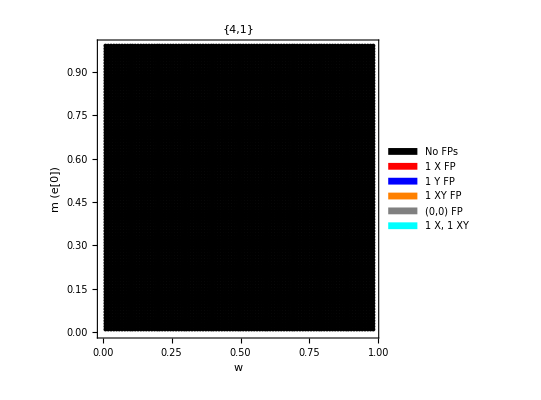
-Graphics-
{RGBColor[1, 0.5, 0],GrayLevel[0],RGBColor[1, 0, 0]}

```mathematica
(*Main: Write the system and parameters, and make our chart.*)
Module[{system, 
dprime = 0.001, v = 1000,
α = 1, β = 1, bv = 4, dv = 1,
minM = 0.01, maxM =0.99, stepM = 0.01,
minW = 0.01, maxW =0.99, stepW = 0.01},

(*See main text for model description.*)
system = {
b0/2 * 1/(x+y)*(x^2 (α + β - α β) + (α + β) x y) - x (d0 + 2 dprime v (x + y))/w+ m y,
b0/2 * 1/(x+y)*(y^2  + (2 - α - β) x y + (1 - α) (1 - β) x^2) - y (d0 + 2 dprime v (x + y)) - m y
};

(*Also, consider making this into a ParallelTable over the bv and dv values of interest!*)
makeChart[system, bv, dv,
minM, maxM, stepM,
minW, maxW, stepW
 ]
]
```